Import packages

```mathematica
SetDirectory[NotebookDirectory[]];
dir=NotebookDirectory[];
figdir=dir<>"../figures/";
datadir=dir<>"../data/";
module dir="/home/james/Code/PhD/source/threeeyedfish/threeeyedfish/source/";
AppendTo[$Path,module dir];
module dir2="/home/james/Code/threeeyedfish/source/";
AppendTo[$Path,module dir2];
<<useful_functions.m
Notation`AutoLoadNotationPalette=False;(*stops the Notation palette from opening*)
<<JoeMatica_OperatorAlgebraNew.m

(*make conjugate print out as a star*)
Unprotect[Conjugate];
Conjugate/:MakeBoxes[Conjugate[x_],StandardForm]:=TemplateBox[{Parenthesize[x,StandardForm,Power]},"Conjugate",DisplayFunction->(SuperscriptBox[#1,"*"]&)]
Protect[Conjugate];
```

Bell checks

```mathematica
(*11, 10, 01, 00*)
v=({{Subscript[c, 1,1]}, {Subscript[c, 1,0]}, {Subscript[c, 0,1]}, {Subscript[c, 0,0]}});
σm1=({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}});
Print[MatrixForm[v],"->",MatrixForm[σm1.v]];
σm2=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}});
Print[MatrixForm[v],"->",MatrixForm[σm2.v]];
σz1=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
σz2=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}});
Print[MatrixForm[v],"->",MatrixForm[σz1.v]];
Print[MatrixForm[v],"->",MatrixForm[σz2.v]];
```

(c_(1,1)
c_(1,0)
c_(0,1)
c_(0,0))->(0
0
c_(1,1)
c_(1,0))

(c_(1,1)
c_(1,0)
c_(0,1)
c_(0,0))->(0
c_(1,1)
0
c_(0,1))

(c_(1,1)
c_(1,0)
c_(0,1)
c_(0,0))->(c_(1,1)
c_(1,0)
-c_(0,1)
-c_(0,0))

(c_(1,1)
c_(1,0)
c_(0,1)
c_(0,0))->(c_(1,1)
-c_(1,0)
c_(0,1)
-c_(0,0))

```mathematica
L1=1/Sqrt[2] σz1;
L2=1/Sqrt[2] σz2;
L3=a σm1+b σm1†;
L4=a σm2+b σm2†;
L1//MatrixForm
L2//MatrixForm
L3//MatrixForm
L4//MatrixForm
```

(1/(√2) | 0 | 0 | 0
0 | 1/(√2) | 0 | 0
0 | 0 | -1/(√2) | 0
0 | 0 | 0 | -1/(√2))

(1/(√2) | 0 | 0 | 0
0 | -1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 0
0 | 0 | 0 | -1/(√2))

(0 | 0 | b | 0
0 | 0 | 0 | b
a | 0 | 0 | 0
0 | a | 0 | 0)

(0 | b | 0 | 0
a | 0 | 0 | 0
0 | 0 | 0 | b
0 | 0 | a | 0)

```mathematica
bell=({{1/Sqrt[2]}, {0}, {0}, {1/Sqrt[2]}});
bell†.L3†.L4.bell//FullSimplify
bell†.L3†.bell
bell†.L4.bell
bell†.bell
```

{{1/2 (b Conjugate[a]+a Conjugate[b])}}

{{0}}

{{0}}

{{1}}

```mathematica
bell†.L1†.L3.bell//FullSimplify
bell†.L1†.L4.bell//FullSimplify
bell†.L2†.L3.bell//FullSimplify
bell†.L2†.L4.bell//FullSimplify
```

{{0}}

{{0}}

{{0}}

«1 more identical outputs»

Noiseless: σ_- and |1>

```mathematica
p=Exp[-u^2 t];
QFI=D[p,u]^2/p+D[1-p,u]^2/(1-p)/.u->Sqrt[γ1]//FullSimplify
Series[QFI,{t,0,3}]
Series[QFI,{γ1,0,2}]
(-2 γ1 t^2)/(4 t)
```

(4 t^2 γ1)/(-1+ⅇ^(t γ1))

4 t-2 γ1 t^2+(γ1^2 t^3)/3+O[t]^4

4 t-2 t^2 γ1+(t^3 γ1^2)/3+O[γ1]^3

-(t γ1)/2

```mathematica
D[T/t QFI,t]//FullSimplify
```

-(4 T γ1 (1+ⅇ^(t γ1) (-1+t γ1)))/((-1+ⅇ^(t γ1))^2)

```mathematica
Reduce[D[T/t QFI,t]==0,t]//Full
```

(-1+ⅇ^(t γ1)≠0&&T==0)||(C[1]∈ℤ&&-1+ⅇ^(1+ProductLog[C[1],-1/ⅇ])≠0&&γ1≠0&&t==(1+ProductLog[C[1],-1/ⅇ])/γ1)

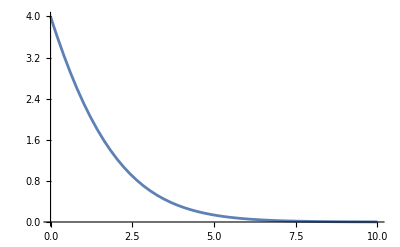

```mathematica
Block[{γ1=1,T=1},Plot[T/t QFI,{t,0,10/γ1},PlotRange->{0,All}]]
```

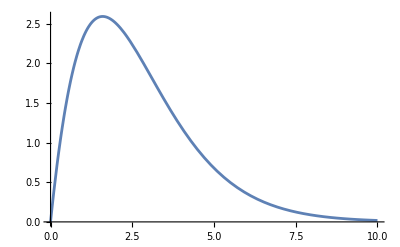

```mathematica
Block[{γ1=1,T=1},Plot[QFI,{t,0,10/γ1},PlotRange->{0,All}]]
```

```mathematica
p=Exp[-4 u^2 t];
QFI=D[p,u]^2/p+D[1-p,u]^2/(1-p)/.u->Sqrt[γ1]//FullSimplify
```

(64 t^2 γ1)/(-1+ⅇ^(4 t γ1))

```mathematica
Limit[QFI,γ1->0]
```

16 t

```mathematica
Series[QFI,{t,0,3}]
```

16 t-32 γ1 t^2+(64 γ1^2 t^3)/3+O[t]^4

```mathematica
Series[QFI,{γ1,0,2}]
```

16 t-32 t^2 γ1+(64 t^3 γ1^2)/3+O[γ1]^3

```mathematica
QFIu=D[p,u]^2/p+D[1-p,u]^2/(1-p)//FullSimplify
Series[QFIu,{u,0,4}]
```

(64 t^2 u^2)/(-1+ⅇ^(4 t u^2))

16 t-32 t^2 u^2+(64 t^3 u^4)/3+O[u]^5

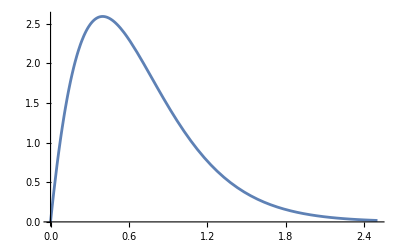

```mathematica
Block[{γ1=1},
Plot[QFI,{t,0,5/(2γ1)},GridLines->{{1/(2γ1)},{}}]
]
```

```mathematica
$Assumptions={γ1>=0,t>=0};
sol=Solve[D[QFI,t]==0]//FullSimplify
sol//N
```

{{γ1→ConditionalExpression[(2+ProductLog[-2/ⅇ^2])/(4 t), t>0]}}

{{γ1→ConditionalExpression[0.398406/t, t>0.]}}

Noiseless: σ_- and |1>, condition on small t

```mathematica
contraction[Subscript[OverHat[bra], j_],Subscript[OverHat[ket], k_],KroneckerDelta[j,k]]
(*contraction[OverHat[σm],Subscript[OverHat[ket], 1],2 Subscript[OverHat[ket], 0]]
contraction[OverHat[σm]^†,Subscript[OverHat[ket], 0],2 Subscript[OverHat[ket], 1]]*)
contraction[OverHat[σm],Subscript[OverHat[ket], 1],Subscript[OverHat[ket], 0]]
contraction[SuperDagger[OverHat[σm]],Subscript[OverHat[ket], 0],Subscript[OverHat[ket], 1]]
contraction[OverHat[σm],Subscript[OverHat[ket], 0],0]
contraction[SuperDagger[OverHat[σm]],Subscript[OverHat[ket], 1],0]

Clear[ℒ]
ℒ[ρ_]:=HoldForm[OverHat[σm]∘ρ∘SuperDagger[OverHat[σm]]-1/2(SuperDagger[OverHat[σm]]∘OverHat[σm]∘ρ+ρ∘SuperDagger[OverHat[σm]]∘OverHat[σm])]
```

```mathematica
ρ̂=Subscript[OverHat[ket], 1]∘Subscript[OverHat[bra], 1];
numer=ℒ[ρ̂]//ReleaseHold//FullSimplify;
(*operator/spectral/induced L2 norm of ||M||*)
M=DiagonalMatrix[Table[Subscript[OverHat[bra], k]∘numer∘Subscript[OverHat[ket], k],{k,0,1}]]//FullSimplify;
numer norm=Max[Sqrt[SingularValueList[M†.M]]]//FullSimplify;
(*release all levels of Hold from leaves to roots*)
denom=ReleaseHold//@ℒ[ℒ[ρ̂]]//FullSimplify;
M=DiagonalMatrix[Table[Subscript[OverHat[bra], k]∘denom∘Subscript[OverHat[ket], k],{k,0,1}]]//FullSimplify;
denom norm=Max[Sqrt[SingularValueList[M†.M]]]//FullSimplify;
(4numer norm)/(Subscript[γ, 1] denom norm)//FullSimplify
```

4/γ_1

Noiseless: a and |n>

```mathematica
fns={
pn[t],
pn1[t],
pn2[t],
pn3[t],
pn4[t],
pn5[t]
};
sol=DSolve[{
pn'[t]==-g n pn[t],pn[0]==1,
pn1'[t]==g (n pn[t]-(n-1) pn1[t]),pn1[0]==0,
pn2'[t]==g ((n-1) pn1[t]-(n-2) pn2[t]),pn2[0]==0,
pn3'[t]==g ((n-2) pn2[t]-(n-3) pn3[t]),pn3[0]==0,
pn4'[t]==g ((n-3) pn3[t]-(n-4) pn4[t]),pn4[0]==0,
pn5'[t]==g ((n-4) pn4[t]-(n-5) pn5[t]),pn5[0]==0
},fns,t]//FullSimplify;
sol//Transpose//TableForm
(fns/.sol)[[1]]==Table[Binomial[n,k] ⅇ^(-g n t)(-1+ⅇ^(g t))^k ,{k,0,5}]//FullSimplify
```

pn[t]→ⅇ^(-g n t)
pn1[t]→ⅇ^(-g n t) (-1+ⅇ^(g t)) n
pn2[t]→1/2 ⅇ^(-g n t) (-1+ⅇ^(g t))^2 (-1+n) n
pn3[t]→1/6 ⅇ^(-g n t) (-1+ⅇ^(g t))^3 (-2+n) (-1+n) n
pn4[t]→1/24 ⅇ^(-g n t) (-1+ⅇ^(g t))^4 (-3+n) (-2+n) (-1+n) n
pn5[t]→1/120 ⅇ^(-g n t) (-1+ⅇ^(g t))^5 (-4+n) (-3+n) (-2+n) (-1+n) n

True

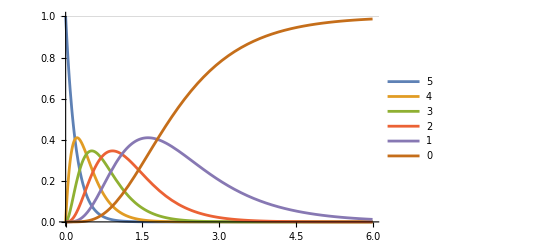

```mathematica
Block[{g=1,n=5},
Plot[
Table[Binomial[n,k] ⅇ^(-g n t)(-1+ⅇ^(g t))^k ,{k,0,n}]//Evaluate,
{t,0,30/(g n)},
PlotLegends->Range[n,0,-1],
PlotRange->{0,1},
GridLines->{{},{1}}
]]
```

```mathematica
Manipulate[
Block[{g=1,n=5},
ListPlot[
Table[{k,Binomial[n,k] ⅇ^(-g n t)(-1+ⅇ^(g t))^k },{k,0,n}]//Evaluate,
PlotRange->{0,1}
]],
{t,(1/10)/(g n),10/(g n)}]
```

```mathematica
addToGlobalAssumptions[{g>=0}]
Clear[p]
(*p[n_,k_]:=Binomial[n,k] ⅇ^(-g n t)(-1+ⅇ^(g t))^k*)
p[n_,k_]:=Binomial[n,k] ⅇ^(-u^2 n t)(-1+ⅇ^(u^2 t))^k
Sum[p[n,k] ,{k,0,n}]
QFI=Sum[D[p[n,k],u]^2/p[n,k] ,{k,0,n}]/.u^2->g//FullSimplify
Series[QFI,{t,0,3}]
Series[QFI,{g,0,3}]
```

1

(4 g n t^2)/(-1+ⅇ^(g t))

4 n t-2 (g n) t^2+1/3 g^2 n t^3+O[t]^4

4 n t-2 (n t^2) g+1/3 n t^3 g^2+O[g]^4

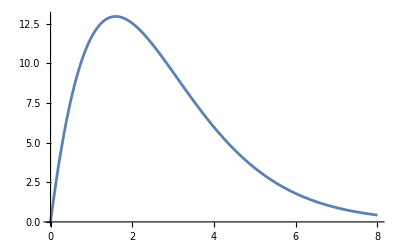

```mathematica
Block[{g=1,n=5},
Plot[QFI,{t,0,40/(g n)}]]
```

```mathematica
Series[Binomial[n,k] ⅇ^(-g n t)(-1+ⅇ^(g t))^k ,{t,0,2}]//FullSimplify
Series[Table[{n-k,Binomial[n,k] ⅇ^(-g n t)(-1+ⅇ^(g t))^k },{k,0,3}],{t,0,2}]//FullSimplify//TableForm
```

(g t)^k (Binomial[n,k]+1/2 g (k-2 n) Binomial[n,k] t+1/24 g^2 (k+3 k^2-12 k n+12 n^2) Binomial[n,k] t^2+O[t]^3)

n | 1-g n t+1/2 g^2 n^2 t^2+O[t]^3
-1+n | g n t+1/2 g^2 (1-2 n) n t^2+O[t]^3
-2+n | 1/2 g^2 (-1+n) n t^2+O[t]^3
-3+n | O[t]^3

```mathematica
{(1/2 g^2 n^2 t^2)/(g n t),(1/2 g^2 (1-2 n) n t^2)/(g n t)}
```

{(g n t)/2,1/2 g (1-2 n) t}

```mathematica
ps={1-u^2 n t,u^2 n t};
Sum[ps[[k]] ,{k,1,2}]
QFI=Sum[D[ps[[k]],u]^2/ps[[k]] ,{k,1,2}]/.u^2->g//FullSimplify
Series[QFI,{t,0,2}]
(4 g n^2 t^2)/(4 n t)
```

1

(4 n t)/(1-g n t)

4 n t+4 g n^2 t^2+O[t]^3

g n t

Noiseless: a and |n>, condition on small t

```mathematica
commutator[â,SuperDagger[â],1] 
contraction[Subscript[OverHat[bra], j_],Subscript[OverHat[ket], k_],KroneckerDelta[j,k]]
contraction[â,Subscript[OverHat[ket], n_],Sqrt[n] Subscript[OverHat[ket], n-1]]
contraction[SuperDagger[â],Subscript[OverHat[ket], n_],Sqrt[n+1] Subscript[OverHat[ket], n+1]]

Clear[ℒ]
ℒ[ρ_]:=HoldForm[â∘ρ∘SuperDagger[â]-1/2(SuperDagger[â]∘â∘ρ+ρ∘SuperDagger[â]∘â)]
```

```mathematica
addToGlobalAssumptions[{n>=2,Element[n,Integers]}]
ρ̂=Subscript[OverHat[ket], n]∘Subscript[OverHat[bra], n];
numer=ℒ[ρ̂]//ReleaseHold//FullSimplify;
(*operator/spectral/induced L2 norm of ||M||*)
M=DiagonalMatrix[Table[Subscript[OverHat[bra], k]∘numer∘Subscript[OverHat[ket], k],{k,n,n-3,-1}]]//FullSimplify;
numer norm=Max[Sqrt[SingularValueList[M†.M]]]//FullSimplify;
(*release all levels of Hold from leaves to roots*)
denom=ReleaseHold//@ℒ[ℒ[ρ̂]]//FullSimplify;
M=DiagonalMatrix[Table[Subscript[OverHat[bra], k]∘denom∘Subscript[OverHat[ket], k],{k,n,n-3,-1}]]//FullSimplify;
denom norm=Max[Sqrt[SingularValueList[M†.M]]]//FullSimplify;
(numer norm)/(denom norm)//FullSimplify
```

1/(-1+2 n)

```mathematica
(*n=1 provides the same bound*)
ρ̂=Subscript[OverHat[ket], 1]∘Subscript[OverHat[bra], 1];
numer=ℒ[ρ̂]//ReleaseHold//FullSimplify;
M=DiagonalMatrix[Table[Subscript[OverHat[bra], k]∘numer∘Subscript[OverHat[ket], k],{k,0,3}]]//FullSimplify;
numer norm=Max[Sqrt[SingularValueList[M†.M]]]//FullSimplify;
denom=ReleaseHold//@ℒ[ℒ[ρ̂]]//FullSimplify;
M=DiagonalMatrix[Table[Subscript[OverHat[bra], k]∘denom∘Subscript[OverHat[ket], k],{k,0,3}]]//FullSimplify;
denom norm=Max[Sqrt[SingularValueList[M†.M]]]//FullSimplify;
(numer norm)/(denom norm)
```

1

```mathematica
ρ̂=Subscript[OverHat[ket], n]∘Subscript[OverHat[bra], n];
finalDM=FullSimplify[MapAll[ReleaseHold,ρ̂+t Subscript[γ, 1] ℒ[ρ̂]+1/4 t^2 Subscript[γ, 1]^2 ℒ[ℒ[ρ̂]]]]
finalDMcoeffs=Table[Subscript[OverHat[bra], k]∘finalDM∘Subscript[OverHat[ket], k],{k,n,n-2,-1}]//FullSimplify
QFI=Sum[(D[finalDMcoeffs[[k]]/.Subscript[γ, 1]->u^2,u]^2)/finalDMcoeffs[[k]] ,{k,1,Length[finalDMcoeffs]}]/.u->Sqrt[Subscript[γ, 1]]//FullSimplify
Series[QFI,{t,0,2}]//FullSimplify
(n (-1+2 n) Subscript[γ, 1] t^2)/(4 n t)
```

1/4 (n∘n (-2+n t γ_1)^2+n t γ_1 ((-1+n) t -2+n∘-2+n γ_1+-1+n∘-1+n (4+(1-2 n) t γ_1)))

{1/4 (-2+n t γ_1)^2,1/4 n t γ_1 (4+(t-2 n t) γ_1),1/4 (-1+n) n t^2 γ_1^2}

(16 n t)/(4+(t-2 n t) γ_1)

4 n t+n (-1+2 n) γ_1 t^2+O[t]^3

1/4 (-1+2 n) t γ_1

Noiseless: Measure-and-reset

```mathematica
addToGlobalAssumptions[{Subscript[γ, 1]>=0,t>=0,Subscript[c, 11]>0,Element[Subscript[b, 1],Complexes]}]
ρ=({{1-Subscript[γ, 1] t Abs[Subscript[c, 11]]^2, Subscript[γ, 1] t Subscript[b, 1]}, {Subscript[γ, 1] t Subscript[b, 1]*, Subscript[γ, 1] t Abs[Subscript[c, 11]]^2}})//FullSimplify;
ρ//MatrixForm
```

(1-t c_11^2 γ_1 | t b_1 γ_1
t Conjugate[b_1] γ_1 | t c_11^2 γ_1)

```mathematica
eig=Eigensystem[ρ]//FullSimplify;
eig//MatrixForm
Series[eig,{t,0,1}]//FullSimplify//MatrixForm
```

(1/2 (1-√(1+4 t γ_1 (-c_11^2+t (Abs[b_1]^2+c_11^4) γ_1))) | 1/2 (1+√(1+4 t γ_1 (-c_11^2+t (Abs[b_1]^2+c_11^4) γ_1)))
{-(-1+2 t c_11^2 γ_1+√(1+4 t γ_1 (-c_11^2+t (Abs[b_1]^2+c_11^4) γ_1)))/(2 t Conjugate[b_1] γ_1),1} | {(1-2 t c_11^2 γ_1+√(1+4 t γ_1 (-c_11^2+t (Abs[b_1]^2+c_11^4) γ_1)))/(2 t Conjugate[b_1] γ_1),1})

(c_11^2 γ_1 t+O[t]^2 | 1-c_11^2 γ_1 t+O[t]^2
{-b_1 γ_1 t+O[t]^2,1} | {1/(Conjugate[b_1] γ_1 t)-(2 c_11^2)/Conjugate[b_1]+b_1 γ_1 t+O[t]^2,1})

```mathematica
unnormv2={1/(Conjugate[Subscript[b, 1]] Subscript[γ, 1] t)-(2 Subscript[c, 11]^2)/Conjugate[Subscript[b, 1]]+Subscript[b, 1] Subscript[γ, 1] t+O[t]^2,1};
Series[Conjugate[Subscript[b, 1]] Subscript[γ, 1] t unnormv2,{t,0,1}]
Series[Norm[%]^2//Normal,{t,0,1}]//FullSimplify
```

{1-2 (c_11^2 γ_1) t+O[t]^2,Conjugate[b_1] γ_1 t+O[t]^2}

1-4 (c_11^2 γ_1) t+O[t]^2

```mathematica
(*manually*)
λ0=1-Subscript[c, 11]^2 Subscript[γ, 1] t;
v0={1,t Subscript[b, 1] *Subscript[γ, 1]};
id=IdentityMatrix[2];
Series[(ρ-λ0 id).v0,{t,0,1}]
```

{O[t]^2,O[t]^2}

```mathematica
λ1=Subscript[c, 11]^2 Subscript[γ, 1] t;
v1={-t Subscript[b, 1] Subscript[γ, 1],1};
id=IdentityMatrix[2];
Series[(ρ-λ1 id).v1,{t,0,1}]
```

{O[t]^2,O[t]^2}

```mathematica
(*orthonormal*)
v0†.v1//Simplify
Series[v0†.v0,{t,0,1}]//Simplify
Series[v1†.v1,{t,0,1}]//Simplify
```

0

1+O[t]^2

1+O[t]^2

```mathematica
Clear[outer]
outer[v1_,v2_]:=Table[v1[[j]]v2†[[k]],{j,1,Length[v1]},{k,1,Length[v1]}]
Clear[proj]
proj[v_]:=outer[v,v]

(*verifying the spectral decomposition*)
ρ==λ0 proj[v0]+λ1 proj[v1]//Series[#,{t,0,1}]&
```

True

```mathematica
ρdot=D[ρ/.Subscript[γ, 1]->u^2,u]/.u->Sqrt[Subscript[γ, 1]];
ρdot//MatrixForm
```

(-2 t c_11^2 √γ_1 | 2 t b_1 √γ_1
2 t Conjugate[b_1] √γ_1 | 2 t c_11^2 √γ_1)

```mathematica
λs={λ0,λ1};
vs={v0,v1};
QFI=Series[FullSimplify[Series[Sum[2/(λs[[j]]+λs[[k]])Abs[vs[[j]]†.ρdot.vs[[k]]]^2,{j,1,2},{k,1,2}],{t,0,1}]],{t,0,2}]
```

4 c_11^2 t+4 c_11^4 γ_1 t^2+O[t]^3

Noisy: Three-level system

```mathematica
Jm=({{0, 0, 0}, {Sqrt[2], 0, 0}, {0, Sqrt[2], 0}});
Jp=Jm†;

Jm.Jm//MatrixForm
Jp.Jm//MatrixForm
Jp.Jp.Jm.Jm//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
2 | 0 | 0)

(2 | 0 | 0
0 | 2 | 0
0 | 0 | 0)

(4 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
ρ=DiagonalMatrix[{p2,p1,p0}];
g1 (Jm.Jm.ρ.Jp.Jp-1/2(Jp.Jp.Jm.Jm.ρ+ρ.Jp.Jp.Jm.Jm))+
g2 (Jm.ρ.Jp-1/2(Jp.Jm.ρ+ρ.Jp.Jm))//Diagonal//FullSimplify//MatrixForm
```

(-2 (2 g1+g2) p2
2 g2 (-p1+p2)
2 g2 p1+4 g1 p2)

```mathematica
probs={p2[t],p1[t],p0[t]};
sol=DSolve[{
p2'[t]==-2 (2 g1+g2) p2[t],
p1'[t]==2 g2 (-p1[t]+p2[t]),
p0'[t]==2 g2 p1[t]+4 g1 p2[t],
p2[0]==1,
p1[0]==0,
p0[0]==0
},probs,t]//FullSimplify;
sol//Transpose//TableForm
probs/.sol//FullSimplify//Transpose//TableForm
```

p0[t]→(ⅇ^(-2 g2 t) (2 ⅇ^(2 g2 t) g1-g2+ⅇ^(-4 g1 t) (-2 g1+g2)))/(2 g1)
p1[t]→(ⅇ^(-2 g2 t) (g2-ⅇ^(-4 g1 t) g2))/(2 g1)
p2[t]→ⅇ^(-2 (2 g1+g2) t)

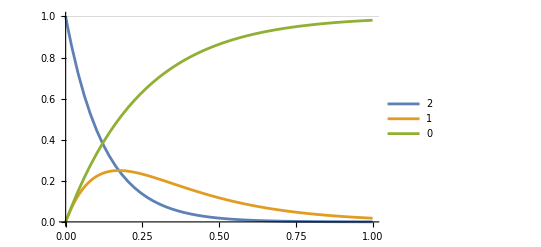

```mathematica
Block[{g1=1,g2=2},
Plot[
probs/.sol//Evaluate,
{t,0,1},
PlotLegends->Range[2,0,-1],
PlotRange->{0,1},
GridLines->{{},{1}}
]
]
```

```mathematica
QFI=Sum[D[p[n,k],u]^2/p[n,k] ,{k,0,n}]/.u^2->g//FullSimplify
Series[QFI,{t,0,3}]
Series[QFI,{g,0,3}]
```

```mathematica
probs1=(probs/.sol[[1]])/.g1->u^2;
QFI=Sum[D[probs1[[k]],u]^2/probs1[[k]] ,{k,1,3}]/.u->Sqrt[g1]//FullSimplify
Series[QFI,{t,0,2}]//FullSimplify
Series[QFI,{g1,0,1}]//FullSimplify
```

2 ⅇ^(-2 (2 g1+g2) t) g1 (32 t^2+(g2 (-1+ⅇ^(4 g1 t)-4 g1 t)^2)/((-1+ⅇ^(4 g1 t)) g1^3)+((8 g1^2 t+g2 (-1+ⅇ^(4 g1 t)-4 g1 t))^2)/(g1^3 (2 (-1+ⅇ^(2 (2 g1+g2) t)) g1+g2-ⅇ^(4 g1 t) g2)))

16 t-(8 (4 g1^2+2 g1 g2+g2^2) t^2)/g1+O[t]^3

-(32 (t^2 (2+g2 (t-ⅇ^(-2 g2 t) t))) g1)/(1-ⅇ^(2 g2 t)+2 g2 t)+O[g1]^2

```mathematica
(*t << *)16/((8 (4 g1^2+2 g1 g2+g2^2))/g1)//FullSimplify
```

(2 g1)/(4 g1^2+2 g1 g2+g2^2)

```mathematica
Series[QFI,{t,0,2},{g1,0,2}]//FullSimplify
Series[QFI,{g1,0,2},{t,0,2}]//FullSimplify
```

16 t+(-(8 g2^2)/g1-16 g2-32 g1+O[g1]^3) t^2+O[t]^3

(32/g2^2-(64 t)/(3 g2)+(320 t^2)/9+O[t]^3) g1+(-64/(g2^4 t)+64/(3 g2^3)-(448 t)/(3 g2^2)+(21184 t^2)/(135 g2)+O[t]^3) g1^2+O[g1]^3

```mathematica
(*cursed, but what is the condition?*)
Limit[QFI,g1->0]
(*since if the time is short enough then it is not cursed*)
Limit[Series[QFI,{t,0,1}]//Normal,g1->0]
```

0

16 t

```mathematica
Series[QFI,{g1,0,1},{t,0,1}]//FullSimplify
Series[QFI,{t,0,1},{g1,0,1}]//FullSimplify
```

(32/g2^2-(64 t)/(3 g2)+O[t]^2) g1+O[g1]^2

16 t+O[t]^2

```mathematica
noiselessQFI=Limit[QFI,g2->0]//FullSimplify
Series[noiselessQFI,{t,0,2}]//FullSimplify
Series[noiselessQFI,{g1,0,1}]//FullSimplify
```

(64 g1 t^2)/(-1+ⅇ^(4 g1 t))

16 t-32 g1 t^2+O[t]^3

16 t-32 t^2 g1+O[g1]^2

```mathematica
(*correction to the lossless QFI*)
Series[QFI,{g2,0,1}]//FullSimplify
Series[QFI,{g2,0,1},{t,0,2}]//FullSimplify
%//Normal//FullSimplify
```

(64 g1 t^2)/(-1+ⅇ^(4 g1 t))-(2 ((-1+Coth[2 g1 t]) (1+16 g1^3 t^3-Cosh[4 g1 t]+16 g1^3 t^3 Coth[2 g1 t])) g2)/g1^2+O[g2]^2

(16 t-32 g1 t^2+O[t]^3)+(-16 t^2+O[t]^3) g2+O[g2]^2

-16 t (-1+2 g1 t+g2 t)

```mathematica
Series[Limit[QFI,g2->0],{g1,0,1}]//FullSimplify
```

16 t-32 t^2 g1+O[g1]^2

```mathematica
Series[QFI,{g1,0,1},{g2,0,1}]//FullSimplify
```

(32/g2^2-(64 t)/(3 g2)+(320 t^2)/9-(7136 t^3 g2)/135+O[g2]^2) g1+O[g1]^2

```mathematica
Series[QFI,{g1,0,2}]//FullSimplify
Series[QFI,{g1,0,2},{t,0,1}]//FullSimplify
```

-(32 (t^2 (2+g2 (t-ⅇ^(-2 g2 t) t))) g1)/(1-ⅇ^(2 g2 t)+2 g2 t)-(64 (ⅇ^(-2 g2 t) t^3 (-2 ⅇ^(2 g2 t) g2 t (9+2 g2 t)+ⅇ^(4 g2 t) (12+5 g2 t)+g2 t (1+8 g2 t))) g1^2)/(3 (-1+ⅇ^(2 g2 t)-2 g2 t)^2)+O[g1]^3

(32/g2^2-(64 t)/(3 g2)+O[t]^2) g1+(-64/(g2^4 t)+64/(3 g2^3)-(448 t)/(3 g2^2)+O[t]^2) g1^2+O[g1]^3

```mathematica
(*condition on small g1, should be an Abs[.] here, putting in a minus by inspection*)
(*(-(64 (ⅇ^(-2 g2 t) t^3 (-2 ⅇ^(2 g2 t) g2 t (9+2 g2 t)+ⅇ^(4 g2 t) (12+5 g2 t)+g2 t (1+8 g2 t))) g1^2)/(3 (-1+ⅇ^(2 g2 t)-2 g2 t)^2))/(-(32 (t^2 (2+g2 (t-ⅇ^(-2 g2 t) t))) g1)/(1-ⅇ^(2 g2 t)+2 g2 t))(* << 1*)//FullSimplify*)
(*g1 << *)(-(-(32 (t^2 (2+g2 (t-ⅇ^(-2 g2 t) t))))/(1-ⅇ^(2 g2 t)+2 g2 t)))/(-(64 (ⅇ^(-2 g2 t) t^3 (-2 ⅇ^(2 g2 t) g2 t (9+2 g2 t)+ⅇ^(4 g2 t) (12+5 g2 t)+g2 t (1+8 g2 t))))/(3 (-1+ⅇ^(2 g2 t)-2 g2 t)^2))//FullSimplify
Series[%,{t,0,5}]//FullSimplify
```

-(3 (-1+ⅇ^(2 g2 t)-2 g2 t) (-g2 t+ⅇ^(2 g2 t) (2+g2 t)))/(2 t (2 ⅇ^(2 g2 t) g2 t (9+2 g2 t)-ⅇ^(4 g2 t) (12+5 g2 t)-g2 t (1+8 g2 t)))

(g2^2 t)/2-(g2^3 t^2)/6-(2 g2^4 t^3)/3+(17 g2^5 t^4)/30+(17 g2^6 t^5)/30+O[t]^6

3-level system: Condition on short time t

```mathematica
(*TODO: derive condition from operator/spectral norm*)
```

L1  herm  L2  nonHerm

```mathematica
addToGlobalAssumptions[{ra>=0,rb>=0,Element[θa,Reals],Element[θb,Reals]}]
L2=({{0, ra Exp[I θa]}, {rb Exp[I θb], 0}});
Eigensystem[L2]//FullSimplify
Tr[L2†.L2]//FullSimplify
```

{{-ⅇ^(1/2 ⅈ (θa+θb)) √(ra rb),ⅇ^(1/2 ⅈ (θa+θb)) √(ra rb)},{{-ⅇ^(1/2 ⅈ (θa-θb)) √(ra/rb),1},{ⅇ^(1/2 ⅈ (θa-θb)) √(ra/rb),1}}}

ra^2+rb^2

```mathematica
v1=Eigenvectors[L2][[1]]//Normalize//FullSimplify
v2=Eigenvectors[L2][[2]]//Normalize//FullSimplify
```

{-ⅇ^(1/2 ⅈ (θa-θb)) √(ra/(ra+rb)),√(rb/(ra+rb))}

{ⅇ^(1/2 ⅈ (θa-θb)) √(ra/(ra+rb)),√(rb/(ra+rb))}

Redo α, β calculation for γ>0

```mathematica
addToGlobalAssumptions[{p∈Reals,q∈Reals,t>=0,γ>=0}]
```

```mathematica
(*(Kdot - i h K)^†*)
a1=(-I p 1/2 γ-Sqrt[γ])t SuperDagger[L̂]∘L̂+c Sqrt[γ]t SuperDagger[L̂]+I p;
a2=t^(3/2)c*1/2 γ SuperDagger[L̂]∘L̂+(1+I q Sqrt[γ])Sqrt[t] SuperDagger[L̂]-Sqrt[t]c*;
(*K*)
b1=1-t 1/2 γ SuperDagger[L̂]∘L̂;
b2=Sqrt[γ]Sqrt[t] L̂;
β=I(a1∘b1+a2∘b2)//FullSimplify;
α=a1∘SuperDagger[a1]+a2∘SuperDagger[a2]//FullSimplify;
```

```mathematica
Collect[Limit[β,{p->0,q->0}],t,FullSimplify]
Collect[Limit[α,{p->0,q->0}],t,FullSimplify]
```

Limit::alimvs: Warning: Assumptions that involve the limit variables are ignored.

1/2 ⅈ t^2 γ^(3/2) (Conjugate[c] (L̂)^†∘L̂∘L̂-c (L̂)^†∘(L̂)^†∘L̂+(L̂)^†∘L̂∘(L̂)^†∘L̂)-ⅈ t √γ (Conjugate[c] L̂-c (L̂)^†)

Limit::alimvs: Warning: Assumptions that involve the limit variables are ignored.

-1/2 t^2 γ (Conjugate[c] (L̂)^†∘L̂∘L̂+c (L̂)^†∘(L̂)^†∘L̂-2 (L̂)^†∘L̂∘(L̂)^†∘L̂)+1/4 c t^3 γ^2 Conjugate[c] (L̂)^†∘L̂∘(L̂)^†∘L̂+t ((L̂)^†∘L̂+Conjugate[c] (c-L̂)-c (L̂)^†)

```mathematica
Collect[β,t,FullSimplify]
Collect[α,t,FullSimplify]
```

-p+1/4 ⅈ t^2 γ^(3/2) (2 Conjugate[c] (L̂)^†∘L̂∘L̂-2 c (L̂)^†∘(L̂)^†∘L̂+(2+ⅈ p √γ) (L̂)^†∘L̂∘(L̂)^†∘L̂)+t ((p-q) γ (L̂)^†∘L̂-ⅈ √γ (Conjugate[c] L̂-c (L̂)^†))

p^2+1/4 c t^3 γ^2 Conjugate[c] (L̂)^†∘L̂∘(L̂)^†∘L̂+1/4 t^2 γ (-2 ⅈ (-ⅈ+(p+q) √γ) Conjugate[c] (L̂)^†∘L̂∘L̂+2 ⅈ c (ⅈ+(p+q) √γ) (L̂)^†∘(L̂)^†∘L̂+(4+p^2 γ) (L̂)^†∘L̂∘(L̂)^†∘L̂)+t ((1-p^2 γ+q^2 γ) (L̂)^†∘L̂+Conjugate[c] (c+ⅈ (ⅈ+(p+q) √γ) L̂)-ⅈ c (-ⅈ+(p+q) √γ) (L̂)^†)

```mathematica
{Table[t^n,{n,0,2}],CoefficientList[β,t]}//FullSimplify//Transpose//TableForm
```

1 | -p
t | (p-q) γ (L̂)^†∘L̂-ⅈ √γ (Conjugate[c] L̂-c (L̂)^†)
t^2 | 1/4 ⅈ γ^(3/2) (2 Conjugate[c] (L̂)^†∘L̂∘L̂-2 c (L̂)^†∘(L̂)^†∘L̂+(2+ⅈ p √γ) (L̂)^†∘L̂∘(L̂)^†∘L̂)

```mathematica
{Table[t^n,{n,0,3}],CoefficientList[α,t]}//FullSimplify//Transpose//TableForm
```

1 | p^2
t | (1-p^2 γ+q^2 γ) (L̂)^†∘L̂+Conjugate[c] (c+ⅈ (ⅈ+(p+q) √γ) L̂)-ⅈ c (-ⅈ+(p+q) √γ) (L̂)^†
t^2 | 1/4 γ (-2 ⅈ (-ⅈ+(p+q) √γ) Conjugate[c] (L̂)^†∘L̂∘L̂+2 ⅈ c (ⅈ+(p+q) √γ) (L̂)^†∘(L̂)^†∘L̂+(4+p^2 γ) (L̂)^†∘L̂∘(L̂)^†∘L̂)
t^3 | 1/4 c γ^2 Conjugate[c] (L̂)^†∘L̂∘(L̂)^†∘L̂